```mathematica
g[y_]=D[rbar((1+y)/(1-y))^(1/α),y];
F[y_]=Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2];
```

80.812

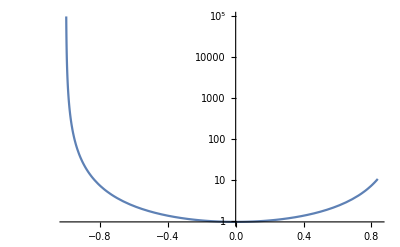

(0.500776 0.000775601^(-1+1/α) rbar)/α

```mathematica
rbar=3;α=4;
g[-0.99845]
LogPlot[F[y],{y,-0.99845,0.83735},PlotRange->All]
Clear[rbar,α]
```

```mathematica
(* This is the mapping with Surkus variable, as discussed in the paper *)
g[y_]=D[rbar((1+y)/(1-y))^(1/α),y];

(* g[y] for exponential mapping *)
g[y_]=1/(1+y α);

(* g[y] for quadratic mapping *)
(* g[y_]=1/(√(1+2 y α));*)

(* This choice uses inverse coordinate, and makes the additional term null *)
(* g[y_]=b(-a/y-(1-a y)/y^2);*)

Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2,{y>0,α>0}]
```

α^2/(4 (1+y α)^2)

```mathematica
Clear[g]
g[y_]=a/(y+b)^2;
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2
```

0

```mathematica
DSolve[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2==0,g[y],y]
```

{{g[y]→C[2]/(y+2 C[1])^2}}

```mathematica
Series[(1-w/Rmax^2) r+w(1/(Rmax-r)-1/Rmax),{r,0,2}]
```

r+(w r^2)/Rmax^3+O[r]^3

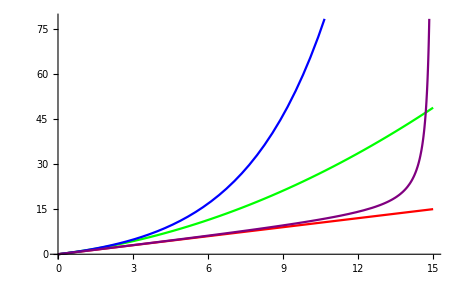

```mathematica
α=0.3;
Plot[{r,r+α/2 r^2,(ⅇ^(α r)-1)/α,((1-w/Rmax^2) r+w(1/(Rmax-r)-1/Rmax))/.{Rmax->15,w->10}},{r,0,15},PlotStyle->{Red,Green,Blue,Purple}]
Clear[α]
```

```mathematica
(* g[y] for exponential mapping *)
1/(1+y α);

(* g[y] for quadratic mapping *)
1/(√(1+2 y α));
```

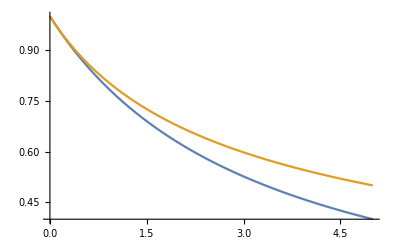

```mathematica
α=0.3;
Plot[{1/(1+y α),1/(√(1+2 y α))},{y,0,5}]
Clear[α]
```

```mathematica
Series[(f[x+h]-2f[x]+f[x-h])/h^2,{h,0,2}]
```

f''[x]+1/12 f^(4)[x] h^2+O[h]^3

```mathematica
f[x+h]==f[x](2-q[x] h^2)-f[x-h]
```

```mathematica
(f[x+h]-2f[x]+f[x-h])/h^2==-q[x]f[x]
```

```mathematica
Solve[y==r+(r/re)^2,r]//Simplify
```

{{r→-1/2 re (re+√(re^2+4 y))},{r→1/2 re (-re+√(re^2+4 y))}}

```mathematica
D[(-1+ⅇ^(y/rRef)) rRef,y]
```

ⅇ^(y/rRef)

```mathematica
g[y_]=ⅇ^(y/rRef);
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2//Simplify
Clear[g]
```

-1/(4 rRef^2)

```mathematica
Series[re/α((1+r/re)^α-1),{α,0,2}]
```

re Log[1+r/re]+1/2 re Log[1+r/re]^2 α+1/6 re Log[1+r/re]^3 α^2+O[α]^3

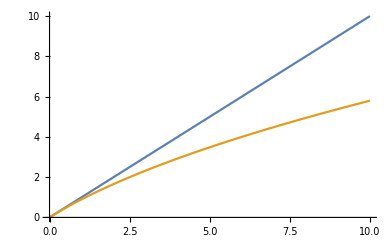

```mathematica
re=2;
Plot[{r,2re(√(1+r/re)-1)},{r,0,10}]
Clear[re]
```

```mathematica
Solve[y==2re(√(1+r/re)-1),r]
g[y_]=D[(4 re y+y^2)/(4 re),y]
g''[y]/(2g[y])-3/4(g'[y]/g[y])^2//Simplify
Clear[g]
```

{{r→(4 re y+y^2)/(4 re)}}

(4 re+2 y)/(4 re)

-3/(4 (2 re+y)^2)

```mathematica
Simplify[Solve[y==rRef Log[1+r/rRef],r],{y>0,r>0,rRef>0}]
```

{{r→(-1+ⅇ^(y/rRef)) rRef}}

```mathematica
Clear[U,Q]
```

```mathematica
r[y_]= y^(1/6);
U=Cn/r[y]^6;
Q=2μ(energy-U);
g[y_]=r'[y];
g[y]^2 Q+(g''[y]/(2g[y])-3/4(g'[y]/g[y])^2)//Expand
Normal[Series[%,{y,∞,0}]];
```

35/(144 y^2)-(Cn μ)/(18 y^(8/3))+(energy μ)/(18 y^(5/3))

```mathematica
(* Long-range behaviour of Qtilde *)
(* From eq. 31 and 32 in the paper *)
r[y_]=rbar((1+y)/(1-y))^(1/α);
g[y_]=D[r[y],y];
F[y_]=Simplify[g''[y]/(2g[y])-3/4(g'[y]/g[y])^2];
U[y_]=De-Cn/r[y]^n;
energy=De-ϵ;
Q=(2μ)/ℏ^2(energy-U[y]);
Qtilde=g[y]^2 Q +F[y];
```

```mathematica
qq=Simplify[α^2 Qtilde/.{ℏ->1}]
```

(-1+α^2+8 rbar^2 ((1+y)/(1-y))^(2/α) (Cn (rbar ((1+y)/(1-y))^(1/α))^-n-ϵ) μ)/((-1+y^2)^2)

```mathematica
Simplify[D[qq,y]]
```

1/((-1+y^2)^3 α)(rbar ((1+y)/(1-y))^(1/α))^-n (16 rbar^2 ((1+y)/(1-y))^(2/α) (Cn (-2+n)+2 (rbar ((1+y)/(1-y))^(1/α))^n ϵ) μ-4 y α (-(rbar ((1+y)/(1-y))^(1/α))^n+(rbar ((1+y)/(1-y))^(1/α))^n α^2+8 Cn rbar^2 ((1+y)/(1-y))^(2/α) μ-8 (rbar ((1+y)/(1-y))^(1/α))^(2+n) ϵ μ))

{y→0.994681}

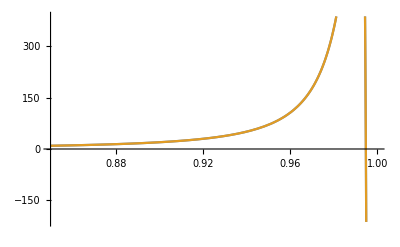

```mathematica
ℏ=2;μ=1; rbar=1;Cn=0;
α=2;n=6;ϵ=0.004;
FindRoot[-8 rbar^2 ((1+y)/(1-y))^(2/α) ϵ μ+(-1+α^2) ℏ^2==0,{y,0.985}]
Plot[{Qtilde,(-8 rbar^2 ((1+y)/(1-y))^(2/α) ϵ μ+(-1+α^2) ℏ^2)/((-1+y)^2 (1+y)^2 α^2 ℏ^2)},{y,0.85,1}]
Clear[α,n,rbar,μ,ℏ,ϵ,Cn]
```

```mathematica
Simplify[Qtilde/.Cn->0]
```

(-8 rbar^2 ((1+y)/(1-y))^(2/α) ϵ μ+(-1+α^2) ℏ^2)/((-1+y)^2 (1+y)^2 α^2 ℏ^2)

```mathematica
Solve[-8 rbar^2 (2/(1-y))^(2/α) ϵ μ+(-1+α^2) ℏ^2==0,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→((2^(-3-2/α) (-ℏ^2+α^2 ℏ^2))/(rbar^2 ϵ μ))^(-α/2) (-1+((2^(-3-2/α) (-ℏ^2+α^2 ℏ^2))/(rbar^2 ϵ μ))^(α/2))}}

```mathematica
Normal[Series[(1+y)^(2/α),{y,1,1}]]/(1-y)^(2/α)//Simplify
```

(4^(1/α) (1-y)^(-2/α) (-1+y+α))/α

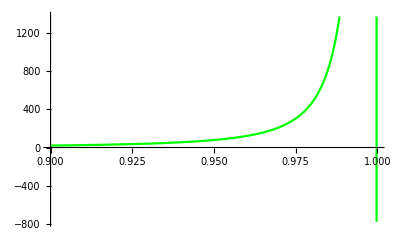

{y→0.999733}

```mathematica
(* eq. 34 of the paper *)
α=2;
ϵ=0.0001;
Plot[{-ϵ (1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y^2)^2)},{y,0.9,1},PlotStyle->{Red,Green}]
FindRoot[-ϵ (1+y)^(2/α-2)/(1-y)^(2/α+2)+(1-1/α^2)/((1-y)(1+y))^2==0,{y,0.9999}]
Clear[α,ϵ]
```

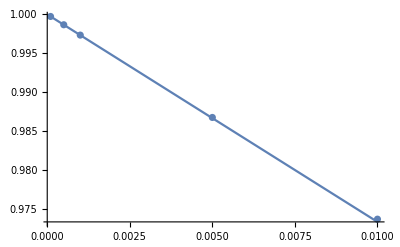

```mathematica
α=2;
(* For α=2, {ϵ, y0}*)
{{0.01,0.9736842105263158},{0.005,0.9867549668874172},{0.001,0.9973368841544618},{0.0005,0.9986675549633578},{0.0001,0.9997333688841488}};
ListPlot[%,PlotRange->All];
Plot[1-((2^(2-2/α) (1/4-1/(4 α^2)))/ϵ)^(-α/2),{ϵ,0.0001,0.01},PlotRange->All];
Show[%,%%,PlotRange->All]
Clear[α]
```

```mathematica
Simplify[Normal[Series[1-((2^(2-2/α) (1/4-1/(4 α^2)))/ϵ)^(-α/2),{α,∞,0}]],ϵ>0]
```

1-2 ⅇ^((1+2 α^2)/(4 α^3)) ϵ^(α/2)

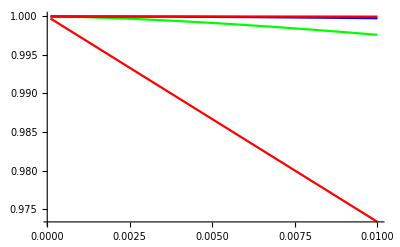

```mathematica
expr=1-2 α^α (-1+α^2)^(-α/2) ϵ^(α/2);
Plot[{expr/.α->2,expr/.α->3,expr/.α->4,(1-2 ⅇ^((1+2 α^2)/(4 α^3)) ϵ^(α/2))/.α->5},{ϵ,0.0001,0.01},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

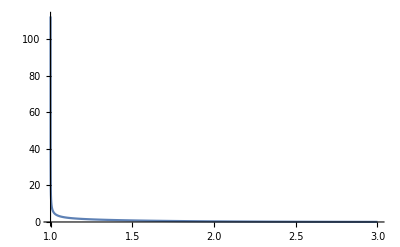

```mathematica
Plot[(-1+α^2)^(-α/2),{α,0,3},PlotRange->All]
```

```mathematica
Series[(-1+α^2)^(-α/2),{α,0,2},Assumptions->{α>0}]
```

1-1/2 ⅈ π α-(π^2 α^2)/8+O[α]^3